# Technologie informacyjne i komunikacyjne

## Mathematica – przykłady: analiza danych doświadczalnych.

Bartłomiej Zglinicki

## Przykład 1. Dane bez niepewności pomiaru.

Poniższe polecenie usuwa wszystkie istniejące definicje w bieżącej sesji programu Mathematica. Wydajemy je tutaj, by zapobiec ewentualnym konfliktom nazw w czasie wykonywania obliczeń.

```mathematica
Clear["Global`*"]
```

## Wczytanie danych doświadczalnych.

### Wczytujemy dane z pliku tekstowego.

Funkcja SetDirectory pozwala wybrać katalog roboczy. Zazwyczaj wygodnie jest umieścić wszystkie pliki, do których będziemy się odwoływać w notatniku, w jednym folderze, a następnie ustawić ten folder jako katalog roboczy – dzięki temu unikniemy konieczności podawania ścieżek dostępu do plików.
Plik dane1.txt, zawierający dane, które będziemy analizować, znajduje się w tym samym folderze, w którym zapisany jest notatnik, dlatego jako katalog roboczy wybieramy właśnie ten folder – jego ścieżkę zwraca funkcja NotebookDirectory.

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\FUW\Dydaktyka\2023Z\TIK\Mathematica\Przyklady\Przyklad-1

Dane z pliku tekstowego wczytujemy posługując się funkcją Import. Jej pierwszym argumentem jest nazwa pliku z danymi (gdybyśmy wcześniej nie ustawili folderu zawierającego ten plik jako katalogu roboczego, musielibyśmy teraz podać pełną ścieżkę pliku, a nie tylko samą jego nazwę), zaś drugim – łańcuch tekstowy “Data” (drugi argument o takiej wartości spowoduje, że dane będą przechowywane w notatniku w postaci tabelarycznej, najbardziej odpowiedniej do naszych celów). Wczytane dane zapisujemy w zmiennej data.

```mathematica
data=Import["dane1.txt", "Data"]
```

{{-0.09,-0.06608},{-0.08,-0.05885},{-0.07,0.11019},{-0.06,0.11501},{-0.05,0.1199},{-0.04,-0.02969},{-0.03,-0.02232},{-0.02,-0.01492},{-0.01,-0.00748},{0,0},{0.01,0.00752},{0.02,0.01508},{0.03,0.02269},{0.04,0.03034},{0.05,0.03803},{0.06,-0.06097},{0.07,0.11019},{0.08,0.11713},{0.09,0.06924},{0.1,-0.04777},{0.11,-0.03793},{0.12,-0.0281},{0.13,0.04181},{0.14,0.0508},{0.15,0.05982},{0.16,0.1255},{0.17,0.13369},{0.18,0.14192},{0.19,0.13882},{0.2,0.14728},{0.21,-0.04007},{0.22,-0.0286},{0.23,0.14465},{0.24,0.15363},{0.25,0.16263},{0.26,0.01709},{0.27,0.02845},{0.28,0.03978},{0.29,0.05107},{0.3,0.06233},{0.31,0.07354},{0.32,0.0847},{0.33,0.09581},{0.34,0.10687},{0.35,0.11787},{0.36,0.02207},{0.37,0.19632},{0.38,0.20624},{0.39,0.1612},{0.4,0.04691},{0.41,0.05934},{0.42,0.07164},{0.43,0.14387},{0.44,0.15504},{0.45,0.1661},{0.46,0.23367},{0.47,0.2436},{0.48,0.25341},{0.49,0.24592},{0.5,0.25574},{0.51,0.21053},{0.52,0.096},{0.53,0.1081},{0.54,0.12001},{0.55,0.19176},{0.56,0.20239},{0.57,0.21282},{0.58,0.2797},{0.59,0.28886},{0.6,0.29781},{0.61,0.29522},{0.62,0.30395},{0.63,0.11663},{0.64,0.12789},{0.65,0.30069},{0.66,0.30899},{0.67,0.31705},{0.68,0.17034},{0.69,0.18027},{0.7,0.18993},{0.71,0.19931},{0.72,0.2084},{0.73,0.21721},{0.74,0.22572},{0.75,0.23394},{0.76,0.24186},{0.77,0.24948},{0.78,0.15007},{0.79,0.32045},{0.8,0.32628},{0.81,0.27691},{0.82,0.15806},{0.83,0.1657},{0.84,0.17299},{0.85,0.23998},{0.86,0.24571},{0.87,0.2511},{0.88,0.31279},{0.89,0.31083},{0.9,0.31444},{0.91,0.26284},{0.92,0.14174},{0.93,0.1471},{0.94,0.15209},{0.95,0.21677},{0.96,0.22017},{0.97,0.22322},{0.98,0.28257},{0.99,0.28406},{1,0.28523},{1.01,0.27471},{1.02,0.2754},{1.03,0.07993},{1.04,0.08294},{1.05,0.24739},{1.06,0.24725},{1.07,0.24679},{1.08,0.09149},{1.09,0.09276},{1.1,0.09371},{1.11,0.09432},{1.12,0.09461},{1.13,0.09458},{1.14,0.09423},{1.15,0.09357},{1.16,0.09261},{1.17,0.09135},{1.18,-0.01694},{1.19,0.1446},{1.2,0.14159},{1.21,0.08344},{1.22,-0.04415},{1.23,-0.04519},{1.24,-0.04653},{1.25,0.01192},{1.26,0.00917},{1.27,0.00618},{1.28,0.0596},{1.29,0.05528},{1.3,0.05075},{1.31,0.02886},{1.32,0.02421},{1.33,-0.03551},{1.34,-0.16457},{1.35,-0.16702},{1.36,-0.16966},{1.37,-0.11244},{1.38,-0.11632},{1.39,-0.12035},{1.4,-0.06788},{1.41,-0.07305},{1.42,-0.07834},{1.43,-0.09507},{1.44,-0.10036},{1.45,-0.30157},{1.46,-0.30405},{1.47,-0.14483},{1.48,-0.14993},{1.49,-0.15508},{1.5,-0.3148},{1.51,-0.31764},{1.52,-0.32052},{1.53,-0.32343},{1.54,-0.32636},{1.55,-0.3293},{1.56,-0.33224},{1.57,-0.33516},{1.58,-0.33806},{1.59,-0.34092},{1.6,-0.45048},{1.61,-0.28986},{1.62,-0.29344},{1.63,-0.35181},{1.64,-0.47926},{1.65,-0.47982},{1.66,-0.4803},{1.67,-0.42064},{1.68,-0.4218},{1.69,-0.42283},{1.7,-0.36708},{1.71,-0.36871},{1.72,-0.37016},{1.73,-0.51029},{1.74,-0.50925},{1.75,-0.50804},{1.76,-0.50666},{1.77,-0.50508},{1.78,-0.5033},{1.79,-0.50132},{1.8,-0.49912},{1.81,-0.60343},{1.82,-0.4374},{1.83,-0.43539},{1.84,-0.48801},{1.85,-0.60954},{1.86,-0.604},{1.87,-0.59824},{1.88,-0.53218},{1.89,-0.52679},{1.9,-0.52112},{1.91,-0.45853},{1.92,-0.45318},{1.93,-0.44752},{1.94,-0.45871},{1.95,-0.45215},{1.96,-0.50018},{1.97,-0.61705},{1.98,-0.60682},{1.99,-0.5963},{2,-0.52545},{2.01,-0.51522},{2.02,-0.50468},{2.03,-0.43719},{2.04,-0.42689},{2.05,-0.41627},{2.06,-0.41666},{2.07,-0.40519},{2.08,-0.58923},{2.09,-0.57414},{2.1,-0.39695},{2.11,-0.38371},{2.12,-0.37014},{2.13,-0.51078},{2.14,-0.49421},{2.15,-0.47734},{2.16,-0.46018},{2.17,-0.44273},{2.18,-0.42499},{2.19,-0.40697},{2.2,-0.38867},{2.21,-0.37009},{2.22,-0.35124},{2.23,-0.43885},{2.24,-0.25609},{2.25,-0.23732},{2.26,-0.27318},{2.27,-0.37795},{2.28,-0.35568},{2.29,-0.33321},{2.3,-0.25048},{2.31,-0.22848},{2.32,-0.20628},{2.33,-0.12723},{2.34,-0.10551},{2.35,-0.0836},{2.36,-0.25735},{2.37,-0.23211},{2.38,-0.04494},{2.39,-0.02189},{2.4,0.0013},{2.41,-0.12991},{2.42,-0.10409},{2.43,-0.07819},{2.44,-0.05221},{2.45,-0.02616},{2.46,-0.0000537197},{2.47,0.0261},{2.48,0.05228},{2.49,0.07849},{2.5,0.10471},{2.51,0.02419},{2.52,0.21378},{2.53,0.23908},{2.54,0.20947},{2.55,0.11065},{2.56,0.13857},{2.57,0.16638},{2.58,0.25412},{2.59,0.28082},{2.6,0.3074},{2.61,0.39048},{2.62,0.4159},{2.63,0.44117},{2.64,0.45492},{2.65,0.48003},{2.66,0.30911},{2.67,0.33678},{2.68,0.526},{2.69,0.55071},{2.7,0.57517},{2.71,0.44484},{2.72,0.47112},{2.73,0.49709},{2.74,0.52272},{2.75,0.54802},{2.76,0.57295},{2.77,0.59752},{2.78,0.62171},{2.79,0.6455},{2.8,0.66889},{2.81,0.58512},{2.82,0.77104},{2.83,0.79225},{2.84,0.75813},{2.85,0.65438},{2.86,0.67695},{2.87,0.699},{2.88,0.78057},{2.89,0.80068},{2.9,0.82025},{2.91,0.89592},{2.92,0.91352},{2.93,0.93056},{2.94,0.92988},{2.95,0.94606},{2.96,0.90677},{2.97,0.7977},{2.98,0.81483},{2.99,0.83129},{3,0.90715},{3.01,0.92143},{3.02,0.93504},{3.03,1.00464},{3.04,1.01604},{3.05,1.02678},{3.06,1.02551},{3.07,1.03508},{3.08,0.84813},{3.09,0.8593},{3.1,1.03153},{3.11,1.0388},{3.12,1.04535},{3.13,0.89666},{3.14,0.90416},{3.15,0.91092},{3.16,0.91692},{3.17,0.92219},{3.18,0.92671},{3.19,0.93048},{3.2,0.9335},{3.21,0.93577},{3.22,0.9373},{3.23,0.83135},{3.24,0.99477},{3.25,0.99319},{3.26,0.93599},{3.27,0.80889},{3.28,0.80786},{3.29,0.80606},{3.3,0.86356},{3.31,0.85939},{3.32,0.8545},{3.33,0.90553},{3.34,0.89251},{3.35,0.8847},{3.36,0.8213},{3.37,0.68806},{3.38,0.68092},{3.39,0.67308},{3.4,0.72458},{3.41,0.71448},{3.42,0.70372},{3.43,0.74895},{3.44,0.73602},{3.45,0.72247},{3.46,0.69697},{3.47,0.6824},{3.48,0.47141},{3.49,0.45865},{3.5,0.60709},{3.51,0.59071},{3.52,0.57379},{3.53,0.40182},{3.54,0.38623},{3.55,0.37012},{3.56,0.35351},{3.57,0.33641},{3.58,0.31883},{3.59,0.30079},{3.6,0.28232},{3.61,0.26342},{3.62,0.24411},{3.63,0.11768},{3.64,0.26099},{3.65,0.23969},{3.66,0.16317},{3.67,0.01718},{3.68,-0.00232},{3.69,-0.02212},{3.7,0.01783},{3.71,-0.0034},{3.72,-0.02487},{3.73,0.0101},{3.74,-0.01265},{3.75,-0.03555},{3.76,-0.07576},{3.77,-0.09865},{3.78,-0.17654},{3.79,-0.32368},{3.8,-0.3441},{3.81,-0.3646},{3.82,-0.3251},{3.83,-0.34657},{3.84,-0.36804},{3.85,-0.33284},{3.86,-0.35512},{3.87,-0.37733},{3.88,-0.41079},{3.89,-0.4326},{3.9,-0.65012},{3.91,-0.66867},{3.92,-0.52529},{3.93,-0.54599},{3.94,-0.56648},{3.95,-0.74127},{3.96,-0.75891},{3.97,-0.7763},{3.98,-0.79343},{3.99,-0.81028},{4,-0.82682},{4.01,-0.84303},{4.02,-0.8589},{4.03,-0.87441},{4.04,-0.88954},{4.05,-1.011},{4.06,-0.86193},{4.07,-0.87669},{4.08,-0.94587},{4.09,-1.08374},{4.1,-1.09432},{4.11,-1.10443},{4.12,-1.054},{4.13,-1.06398},{4.14,-1.07342},{4.15,-1.02566},{4.16,-1.03485},{4.17,-1.04344},{4.18,-1.19027},{4.19,-1.19549},{4.2,-1.2001},{4.21,-1.20409},{4.22,-1.20744},{4.23,-1.21013},{4.24,-1.21217},{4.25,-1.21353},{4.26,-1.32094},{4.27,-1.15755},{4.28,-1.15771},{4.29,-1.21205},{4.3,-1.33482},{4.31,-1.33007},{4.32,-1.32462},{4.33,-1.2584},{4.34,-1.25239},{4.35,-1.24564},{4.36,-1.18149},{4.37,-1.17412},{4.38,-1.16598},{4.39,-1.17423},{4.4,-1.16427},{4.41,-1.20843},{4.42,-1.321},{4.43,-1.30599},{4.44,-1.29027},{4.45,-1.21375},{4.46,-1.19742},{4.47,-1.18034},{4.48,-1.10587},{4.49,-1.08818},{4.5,-1.06973},{4.51,-1.06188},{4.52,-1.04175},{4.53,-1.21673},{4.54,-1.19216},{4.55,-1.00511},{4.56,-0.98162},{4.57,-0.95741},{4.58,-1.08705},{4.59,-1.05909},{4.6,-1.03048},{4.61,-1.00122},{4.62,-0.97133},{4.63,-0.94081},{4.64,-0.90969},{4.65,-0.87795},{4.66,-0.84563},{4.67,-0.81273},{4.68,-0.88601},{4.69,-0.68862},{4.7,-0.65495},{4.71,-0.67564},{4.72,-0.76499},{4.73,-0.72705},{4.74,-0.68867},{4.75,-0.58982},{4.76,-0.55147},{4.77,-0.51271},{4.78,-0.41692},{4.79,-0.37828},{4.8,-0.33926},{4.81,-0.49574},{4.82,-0.45309},{4.83,-0.24838},{4.84,-0.20764},{4.85,-0.16665},{4.86,-0.27996},{4.87,-0.23614},{4.88,-0.19216},{4.89,-0.14803},{4.9,-0.10378},{4.91,-0.05942},{4.92,-0.01499},{4.93,0.02951},{4.94,0.07404},{4.95,0.11858},{4.96,0.05638},{4.97,0.26425},{4.98,0.3078},{4.99,0.2964},{5,0.21572},{5.01,0.26171},{5.02,0.30751},{5.03,0.41316},{5.04,0.45765},{5.05,0.5019},{5.06,0.60253},{5.07,0.64536},{5.08,0.68788},{5.09,0.71873},{5.1,0.76076},{5.11,0.60658},{5.12,0.6508},{5.13,0.85636},{5.14,0.89719},{5.15,0.93755},{5.16,0.82288},{5.17,0.86458},{5.18,0.90571},{5.19,0.94624},{5.2,0.98616},{5.21,1.02543},{5.22,1.06405},{5.23,1.10197},{5.24,1.1392},{5.25,1.17569},{5.26,1.10471},{5.27,1.30307},{5.28,1.33639},{5.29,1.31402},{5.3,1.22166},{5.31,1.25525},{5.32,1.28795},{5.33,1.37979},{5.34,1.40978},{5.35,1.43884},{5.36,1.5236},{5.37,1.54988},{5.38,1.5752},{5.39,1.58237},{5.4,1.60599},{5.41,1.57371},{5.42,1.47122},{5.43,1.4945},{5.44,1.51667},{5.45,1.5978},{5.46,1.61689},{5.47,1.63488},{5.48,1.7084},{5.49,1.72328},{5.5,1.73703},{5.51,1.73831},{5.52,1.74999},{5.53,1.56468},{5.54,1.57703},{5.55,1.74998},{5.56,1.7575},{5.57,1.76385},{5.58,1.61449},{5.59,1.62086},{5.6,1.62602},{5.61,1.62998},{5.62,1.63274},{5.63,1.63429},{5.64,1.63465},{5.65,1.6338},{5.66,1.63176},{5.67,1.62852},{5.68,1.51736},{5.69,1.67513},{5.7,1.66747},{5.71,1.60375},{5.72,1.46971},{5.73,1.46131},{5.74,1.45173},{5.75,1.50104},{5.76,1.48826},{5.77,1.47436},{5.78,1.51598},{5.79,1.49317},{5.8,1.47518},{5.81,1.40123},{5.82,1.25705},{5.83,1.23863},{5.84,1.21913},{5.85,1.25865},{5.86,1.23621},{5.87,1.21278},{5.88,1.24502},{5.89,1.21878},{5.9,1.19162},{5.91,1.1522},{5.92,1.12343},{5.93,0.89795},{5.94,0.87044},{5.95,1.00386},{5.96,0.97221},{5.97,0.93979},{5.98,0.75207},{5.99,0.72052},{6,0.68824},{6.01,0.65525},{6.02,0.62159},{6.03,0.58726},{6.04,0.55231},{6.05,0.51677},{6.06,0.48065},{6.07,0.44399},{6.08,0.30008},{6.09,0.42579},{6.1,0.3868},{6.11,0.2925},{6.12,0.12864},{6.13,0.09122},{6.14,0.05343},{6.15,0.07535},{6.16,0.03605},{6.17,-0.0035},{6.18,0.01338},{6.19,-0.02746},{6.2,-0.06845},{6.21,-0.12671},{6.22,-0.16762},{6.23,-0.26347},{6.24,-0.42852},{6.25,-0.46677},{6.26,-0.50503},{6.27,-0.48319},{6.28,-0.52221},{6.29,-0.56111},{6.3,-0.54323},{6.31,-0.58267},{6.32,-0.6219},{6.33,-0.67221},{6.34,-0.71071},{6.35,-0.94473},{6.36,-0.9796},{6.37,-0.85233},{6.38,-0.88892},{6.39,-0.92507},{6.4,-1.11529},{6.41,-1.14812},{6.42,-1.18045},{6.43,-1.21225},{6.44,-1.2435},{6.45,-1.27415},{6.46,-1.30419},{6.47,-1.33359},{6.48,-1.36232},{6.49,-1.39035},{6.5,-1.52439},{6.51,-1.38756},{6.52,-1.41422},{6.53,-1.49495},{6.54,-1.64402},{6.55,-1.66544},{6.56,-1.68602},{6.57,-1.64568},{6.58,-1.66537},{6.59,-1.68413},{6.6,-1.64529},{6.61,-1.663},{6.62,-1.67971},{6.63,-1.83425},{6.64,-1.84676},{6.65,-1.85825},{6.66,-1.86868},{6.67,-1.87804},{6.68,-1.88632},{6.69,-1.89351},{6.7,-1.89958},{6.71,-2.01126},{6.72,-1.8517},{6.73,-1.85524},{6.74,-1.9125},{6.75,-2.03775},{6.76,-2.03502},{6.77,-2.03114},{6.78,-1.96605},{6.79,-1.9607},{6.8,-1.95415},{6.81,-1.88976},{6.82,-1.88168},{6.83,-1.87238},{6.84,-1.87902},{6.85,-1.867},{6.86,-1.90865},{6.87,-2.01825},{6.88,-1.99984},{6.89,-1.98025},{6.9,-1.89944},{6.91,-1.87838},{6.92,-1.85613},{6.93,-1.77605},{6.94,-1.75232},{6.95,-1.72741},{6.96,-1.71268},{6.97,-1.68526},{6.98,-1.85252},{6.99,-1.81984},{7,-1.62428},{7.01,-1.59187},{7.02,-1.55837},{7.03,-1.67832},{7.04,-1.6403},{7.05,-1.60125},{7.06,-1.5612},{7.07,-1.52016},{7.08,-1.47814},{7.09,-1.43517},{7.1,-1.39126},{7.11,-1.34643},{7.12,-1.30071},{7.13,-1.36085},{7.14,-1.15003},{7.15,-1.10263},{7.16,-1.10932},{7.17,-1.18438},{7.18,-1.13189},{7.19,-1.0787},{7.2,-0.96479},{7.21,-0.91116},{7.22,-0.85689},{7.23,-0.74536},{7.24,-0.69077},{7.25,-0.63563},{7.26,-0.77579},{7.27,-0.71664},{7.28,-0.49526},{7.29,-0.43771},{7.3,-0.37976},{7.31,-0.47598},{7.32,-0.41495},{7.33,-0.35365},{7.34,-0.2921},{7.35,-0.23034},{7.36,-0.1684},{7.37,-0.10631},{7.38,-0.04412},{7.39,0.01816},{7.4,0.08048},{7.41,0.03606},{7.42,0.26174},{7.43,0.32309},{7.44,0.32947},{7.45,0.26655},{7.46,0.33026},{7.47,0.39373},{7.48,0.51699},{7.49,0.57901},{7.5,0.64072},{7.51,0.75871},{7.52,0.81879},{7.53,0.87845},{7.54,0.92631},{7.55,0.98522},{7.56,0.84776},{7.57,0.90854},{7.58,1.13049},{7.59,1.18754},{7.6,1.24392},{7.61,1.14507},{7.62,1.20237},{7.63,1.25889},{7.64,1.31457},{7.65,1.3694},{7.66,1.42334},{7.67,1.47635},{7.68,1.52841},{7.69,1.57949},{7.7,1.62956},{7.71,1.57184},{7.72,1.78317},{7.73,1.82914},{7.74,1.81911},{7.75,1.73876},{7.76,1.78402},{7.77,1.82805},{7.78,1.93086},{7.79,1.97147},{7.8,2.01079},{7.81,2.10544},{7.82,2.14123},{7.83,2.17567},{7.84,2.19158},{7.85,2.22355},{7.86,2.19921},{7.87,2.10426},{7.88,2.13467},{7.89,2.16356},{7.9,2.25099},{7.91,2.27596},{7.92,2.29941},{7.93,2.37795},{7.94,2.39742},{7.95,2.41534},{7.96,2.42034},{7.97,2.4353},{7.98,2.25283},{7.99,2.26758},{8,2.44248},{8.01,2.45151},{8.02,2.45893},{8.03,2.31019},{8.04,2.31673},{8.05,2.32161},{8.06,2.32485},{8.07,2.32644},{8.08,2.32638},{8.09,2.32467},{8.1,2.32133},{8.11,2.31634},{8.12,2.30973},{8.13,2.19475},{8.14,2.34827},{8.15,2.33593},{8.16,2.2671},{8.17,2.12753},{8.18,2.11318},{8.19,2.09723},{8.2,2.13975},{8.21,2.11978},{8.22,2.09829},{8.23,2.13192},{8.24,2.10072},{8.25,2.07396},{8.26,1.99085},{8.27,1.83715},{8.28,1.80883},{8.29,1.77908},{8.3,1.80797},{8.31,1.77457},{8.32,1.73983},{8.33,1.76043},{8.34,1.72222},{8.35,1.68277},{8.36,1.63075},{8.37,1.58907},{8.38,1.3504},{8.39,1.3094},{8.4,1.42907},{8.41,1.38339},{8.42,1.33668},{8.43,1.13442},{8.44,1.0881},{8.45,1.04081},{8.46,0.99259},{8.47,0.94348},{8.48,0.89351},{8.49,0.84273},{8.5,0.79116},{8.51,0.73886},{8.52,0.68585},{8.53,0.52544},{8.54,0.63453},{8.55,0.57877},{8.56,0.46759},{8.57,0.28675},{8.58,0.23224},{8.59,0.17728},{8.6,0.18196},{8.61,0.12536},{8.62,0.06846},{8.63,0.06794},{8.64,0.00968},{8.65,-0.04875},{8.66,-0.12446},{8.67,-0.18281},{8.68,-0.29609},{8.69,-0.47854},{8.7,-0.53415},{8.71,-0.58972},{8.72,-0.58513},{8.73,-0.64134},{8.74,-0.69733},{8.75,-0.69645},{8.76,-0.7528},{8.77,-0.8088},{8.78,-0.87578},{8.79,-0.9308},{8.8,-1.18119},{8.81,-1.23227},{8.82,-1.12105},{8.83,-1.17351},{8.84,-1.22534},{8.85,-1.43105},{8.86,-1.47915},{8.87,-1.52654},{8.88,-1.57317},{8.89,-1.619},{8.9,-1.664},{8.91,-1.70813},{8.92,-1.75136},{8.93,-1.79364},{8.94,-1.83494},{8.95,-1.98196},{8.96,-1.85781},{8.97,-1.89684},{8.98,-1.98964},{8.99,-2.15044},{9,-2.18327},{9.01,-2.21492},{9.02,-2.18531},{9.03,-2.21538},{9.04,-2.24416},{9.05,-2.21498},{9.06,-2.24198},{9.07,-2.26761},{9.08,-2.43067},{9.09,-2.45134},{9.1,-2.47057},{9.11,-2.48837},{9.12,-2.50469},{9.13,-2.51953},{9.14,-2.53286},{9.15,-2.54466},{9.16,-2.66166},{9.17,-2.50699},{9.18,-2.51501},{9.19,-2.57632},{9.2,-2.70519},{9.21,-2.70566},{9.22,-2.70454},{9.23,-2.64177},{9.24,-2.63832},{9.25,-2.63323},{9.26,-2.56985},{9.27,-2.56236},{9.28,-2.55321},{9.29,-2.55956},{9.3,-2.54681},{9.31,-2.5873},{9.32,-2.6953},{9.33,-2.67486},{9.34,-2.65281},{9.35,-2.5691},{9.36,-2.54472},{9.37,-2.51871},{9.38,-2.43446},{9.39,-2.40614},{9.4,-2.37622},{9.41,-2.35606},{9.42,-2.3228},{9.43,-2.48382},{9.44,-2.4445},{9.45,-2.24189},{9.46,-2.20204},{9.47,-2.16071},{9.48,-2.27245},{9.49,-2.22584},{9.5,-2.17784},{9.51,-2.12846},{9.52,-2.07773},{9.53,-2.02567},{9.54,-1.97231},{9.55,-1.91767},{9.56,-1.86178},{9.57,-1.80467},{9.58,-1.8531},{9.59,-1.63026},{9.6,-1.57054},{9.61,-1.56461},{9.62,-1.62677},{9.63,-1.56109},{9.64,-1.49445},{9.65,-1.36683},{9.66,-1.29923},{9.67,-1.23074},{9.68,-1.10477},{9.69,-1.03552},{9.7,-0.96549},{9.71,-0.91188},{9.72,-0.84014},{9.73,-0.82263},{9.74,-0.87368},{9.75,-0.79738},{9.76,-0.72058},{9.77,-0.58329},{9.78,-0.50652},{9.79,-0.42937},{9.8,-0.29524},{9.81,-0.21834},{9.82,-0.19608},{9.83,-0.24277},{9.84,-0.16251},{9.85,-0.08218},{9.86,0.05824},{9.87,0.13774},{9.88,0.21719},{9.89,0.3532},{9.9,0.43156}}

### KROK OPCJONALNY: Przyglądamy się danym doświadczalnym.

Możemy teraz sprawdzić, ile serii pomiarów wykonano – jest ich tyle, ile wierszy ma tablica data. Polecenie Dimensions[data] zwraca wymiary tablicy data w formacie {wiersze, kolumny}, zatem liczba wierszy to Dimensions[data][[1]].

```mathematica
Dimensions[data][[1]]
```

1000

Wyniki n–tej serii pomiarów w postaci listy {x, y} uzyskamy odczytując n–ty wiersz tablicy data za pomocą polecenia data[[n, All]]. Zmierzona w n–tej serii pomiarów wartość wielkości x to zatem data[[n, 1]], zaś wartość wielkości y to data[[n, 2]]. Poniżej dla przykładu sprawdzamy wyniki pierwszej serii pomiarów.

```mathematica
data[[1,All]]
```

{-0.09,-0.06608}

```mathematica
data[[1,1]]
```

-0.09

```mathematica
data[[1, 2]]
```

-0.06608

### Wykreślamy dane doświadczalne.

W celu przedstawienia wyników pomiarów na wykresie musimy posłużyć się funkcją ListPlot. Podając argument ImageSize o wartości Full sprawimy, że wykres zajmie całą szerokość notatnika. Wykres przypisujemy do zmiennej plotData, by móc go potem wyświetlić jeszcze raz, na jednym rysunku wraz z wykresem dopasowanej zależności.

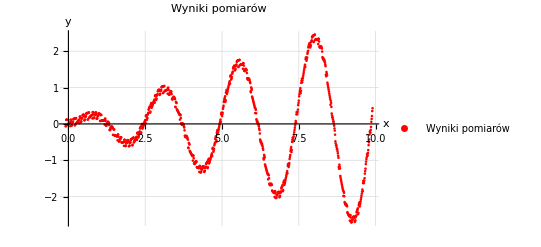

```mathematica
plotData=ListPlot[data,PlotStyle->{Red}, AxesLabel->{x, y}, PlotLabel->Style["Wyniki pomiarów",FontSize->26],LabelStyle->{FontSize->16}, GridLines->Automatic,PlotLegends->Placed[PointLegend[{Red},{"Wyniki pomiarów"}],Below], ImageSize->Full]
```

## Dopasowanie zależności y = f(x) do danych doświadczalnych.

### Definiujemy funkcję f(x), która określa postać dopasowywanej zależności.

O tym, jakiej postaci zależność powinniśmy dopasować do wyników pomiarów, dowiemy się z modelu teoretycznego badanego zjawiska (lub z treści zadania). Jeśli jednak nie dysponujemy tą informacją, możemy spróbować zgadnąć postać dopasowywanej zależności, przyglądając się wykonanemu przed chwilą wykresowi.
Na liście argumentów funkcji, oprócz zmiennej niezależnej x, muszę się także znaleźć parametry dopasowania.

```mathematica
f[x_,a_,b_,c_,d_]:= a x Sin[b x + c] + d
```

### Dopasowujemy zależność y = f(x) do wyników pomiarów.

Mathematica oferuje kilka funkcji, które możemy wykorzystać w celu przeprowadzenia dopasowania. Najbardziej wszechstronną jest funkcja NonlinearModelFit. Jej argumenty to, kolejno, tablica z danymi doświadczalnymi, funkcja określająca dopasowywaną zależność, lista parametrów dopasowania oraz nazwa zmiennej niezależnej.

```mathematica
fit=NonlinearModelFit[data, f[x, a, b, c, d],{a,b,c,d},x]
```

FittedModel[0.0360626-0.29296 x Sin[12.573-2.55094 x]]

Funkcja NonlinearModelFit zwraca skomplikowany obiekt zawierający szczegółowe informacje o wyniku dopasowania. Polecenie fit[“BestFitParameters”] zwróci wyznaczone wartości parametrów dopasowania w postaci listy reguł, natomiast polecenie fit[“ParameterErrors”] – niepewności parametrów w postaci listy liczb (ich kolejność odpowiada kolejności parametrów dopasowania z trzeciego argumentu funkcji NonlinearModelFit).

```mathematica
fit["BestFitParameters"]
```

{a→0.29296,b→2.55094,c→-12.573,d→0.0360626}

```mathematica
fit["ParameterErrors"]
```

{0.00052144,0.000896797,0.00692377,0.00207517}

Dane te możemy przedstawić w postaci czytelnej tabeli, której każdy wiersz zawiera, kolejno, nazwę parametru, jego wyznaczoną w wyniku dopasowania wartość oraz jej niepewność. Tabelę przypisujemy do zmiennej fitParameters, by móc ją później zapisać do pliku.

```mathematica
fitParameters = Transpose[{fit["BestFitParameters"][[All,1]],fit["BestFitParameters"][[All,2]],fit["ParameterErrors"]}]//TableForm
```

a | 0.29296 | 0.00052144
b | 2.55094 | 0.000896797
c | -12.573 | 0.00692377
d | 0.0360626 | 0.00207517

W razie potrzeby z obiektu fit możemy wydobyć jeszcze więcej danych. Szczegółowe informacje o tym, jak to zrobić, można znaleźć w dokumentacji funkcji NonlinearModelFit.

### Wykreślamy dopasowaną zależność.

Obiekt fit możemy potraktować jak zwykłą funkcję: fit[x] odpowiada funkcji, której wykres jest krzywą najlepszego dopasowania.

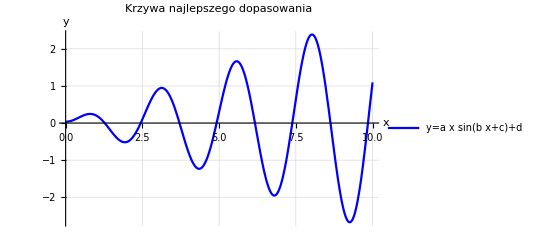

```mathematica
plotFit=Plot[fit[x],{x,0,10}, PlotStyle->{Blue},AxesLabel->{x,y},PlotLabel->Style["Krzywa najlepszego dopasowania",FontSize->26],LabelStyle->{FontSize->16},GridLines->Automatic, PlotLegends->Placed[LineLegend[{Blue},{TraditionalForm[HoldForm[y = a x Sin[b x + c] + d]]}],Below],ImageSize->Full]
```

## Prezentacja wyników dopasowania.

### Wykreślamy wyniki pomiarów i dopasowaną zależność we wspólnym układzie współrzędnych.

Wykorzystamy funkcję Show, by przestawić przygotowane wcześniej osobno wykresy na jednym rysunku, we wspólnym układzie współrzędnych. Wynik jej działania przypiszemy do zmiennej plotAll, by móc go później zapisać do pliku.

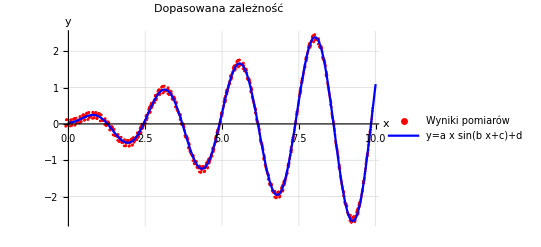

```mathematica
plotAll = Show[plotData,plotFit, AxesLabel->{x,y},PlotLabel->Style["Dopasowana zależność",FontSize->26],LabelStyle->{FontSize->16}, GridLines->Automatic, ImageSize->Full]
```

### Zapisujemy do plików wyznaczone parametry dopasowania oraz wykres.

W obu przypadkach wykorzystamy funkcję Export. Zaczniemy od tabeli zawierającej wyznaczone wartości parametrów dopasowania i ich niepewności, przechowywanej w zmiennej fitParameters. Trzeci argument o wartości “Table” zapewnia przejrzystą postać zawartości utworzonego pliku.

```mathematica
Export["dane1_wyniki.txt",fitParameters, "Table"]
```

dane1_wyniki.txt

```mathematica
Export["dane1_wyniki.pdf", plotAll]
```

dane1_wyniki.pdf